Initial Condition Plots

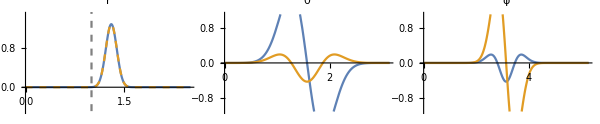

Total Strain Energy:

3221.524183688151434

Displacement Amplitude:
0.0055714636584626796426 R_*

θ Integrals Time:

5.14063 seconds

ϕ Integrals Time:

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {ϕ} = {2.88379}. NIntegrate obtained -2.91434×10^-16 and 3.3226×10^-16 for the integral and error estimates.

0.3125 seconds

NIntegrate::precw: The precision of the argument function (1/2 ⅇ^(«1») r^3 ((3.356978959868571505515511507090947807660521755×10^-17+1.571655128426880305002844062717247711312595120137517013026178×10^-9 ⅈ) SphericalHankelH1[1,0.003095079631367958717995592594565170542783705110417888730823598251 r]+(3.356978959868571505515511507090947807660521755×10^-17-«112» ⅈ) SphericalHankelH2[1,«83» r])) is less than WorkingPrecision (60.).

NIntegrate::precw: The precision of the argument function (1/2 ⅇ^(-72 («1»)^2) r^3 ((2.134145767020809727126869271883289032×10^-23+2.2022232803438160748265050030321075227180605065645204991322×10^-11 ⅈ) SphericalHankelH1[2,0.007732568239757714630504974195617790940656118784946429387951177637 r]+(2.134145767020809727126869271883289032×10^-23-«110» ⅈ) SphericalHankelH2[2,«83» r])) is less than WorkingPrecision (60.).

NIntegrate::precw: The precision of the argument function (1/2 ⅇ^(-72 («1»)^2) r^3 ((3.048705340068032089471242209×10^-30+1.274831213050381536026174738730653635650024252067010736436533×10^-13 ⅈ) SphericalHankelH1[3,0.01132452242300927906264714041021371561834482922355968369816394424 r]+(3.048705340068032089471242209×10^-30-«109» ⅈ) SphericalHankelH2[3,«83» r])) is less than WorkingPrecision (60.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

{12.375,Null}

```mathematica
(* Calculation Parameters *)
lmn=1;
lmx=10;
nmx=10;
workprec=60;
maxrec=10;
accgl=Automatic;
precgl=10;

(* Eigenfrequencies *)
SetDirectory[NotebookDirectory[]];
<<evaluesc370;

(* Model Parameters *)
Rs=1;
c1=1;
c2=370;
μ1=1;
μ2=1/11;
α=(c2 μ1 -c1 μ2)/(c2 μ1 +c1 μ2);
τ=.0123;
zshift=0.766;
Ei=10^46;

(* Probe Parameters *)
rp=1 Rs;
θp=π/2;
ϕp=π+σϕ;

(* Initial Condition Parameters*)
r0=13/10;
σr=1/12;
σθ=1/3`32;
σϕ=1/3`32;

(* Initial Condition *)
r0a=(r0^2-σr^2)/r0;
fr[r_]:=r Exp[-(r-r0a)^2/(2 σr^2)];
fθ[θ_]:=Evaluate[Sin[θ]^2 D[Exp[-(θ-π/2)^2/(2 σθ^2)],{θ,1(*0*)}]](*Sin[θ]^3*)(*1-LegendreP[2,0,Cos[θ]]*);
fϕ[ϕ_]:=Evaluate[D[Exp[-(ϕ-π)^2/(2 σϕ^2)],{ϕ,1}]](*1*);

Uϕ0[r_,θ_,ϕ_]:=fr[r](fθ'[θ]fϕ[ϕ])
Uθ0[r_,θ_,ϕ_]:=-fr[r](fθ[θ]fϕ'[ϕ])/Sin[θ]
fmax=FindMaximum[√(Uθ0[r0,θ,ϕ]^2+Uϕ0[r0,θ,ϕ]^2),{θ,π/2-.2`32},{ϕ,π+.4`32},WorkingPrecision->2 MachinePrecision][[1]];
Uϕ0[r_,θ_,ϕ_]:=fr[r](fθ'[θ]fϕ[ϕ])/fmax
Uθ0[r_,θ_,ϕ_]:=-fr[r](fθ[θ]fϕ'[ϕ])/Sin[θ]/fmax

(* Plot Initial Condition *)
Print["Initial Condition Plots"]
Show[Plot[{fr[r],fr[r]},{r,0,2.5},PlotRange->{-.5,1.5},PlotLabel->"r",PlotStyle->{Default,Dashed}],ListPlot[{{1,-10},{1,10}},Joined->True,PlotStyle->{Dashed,Gray}]];
Plot[{fθ[θ],fθ'[θ]/fmax}//Evaluate,{θ,0,π},PlotRange->{-1.1,1.1},PlotLabel->"θ"];
Plot[{fϕ'[ϕ]/fmax,fϕ[ϕ]}//Evaluate,{ϕ,0,2π},PlotRange->{-1.1,1.1},PlotLabel->"ϕ"];
GraphicsRow[{%%%,%%,%},-5,ImageSize->600]

(* Initial Strain Energy *)
ϵ=10^-10;
wp=20;
rm=8;

frA=NIntegrate[(fr[r])^2,{r,0,rm},WorkingPrecision->wp];
frB=NIntegrate[(r fr'[r]-fr[r])^2,{r,0,rm},WorkingPrecision->wp];

fθA=NIntegrate[Csc[θ](fθ'[θ]-fθ[θ]Cot[θ])^2,{θ,0,π},WorkingPrecision->wp];
fθB=NIntegrate[Csc[θ](fθ[θ])^2,{θ,0,π},WorkingPrecision->wp];
fθC=NIntegrate[Sin[θ](fθ'[θ])^2,{θ,0,π},WorkingPrecision->wp];
fθD=NIntegrate[Sin[θ](fθ''[θ]-fθ'[θ]Cot[θ])^2,{θ,0,π},WorkingPrecision->wp];
fθE=NIntegrate[Csc[θ]^3(fθ[θ])^2,{θ,ϵ,π-ϵ},WorkingPrecision->wp];
fθF=NIntegrate[Csc[θ]fθ[θ](fθ''[θ]-fθ'[θ]Cot[θ]),{θ,0,π},WorkingPrecision->wp];

fϕA=NIntegrate[(fϕ'[ϕ])^2 ,{ϕ,0,2π},WorkingPrecision->wp];
fϕB=NIntegrate[(fϕ[ϕ])^2 ,{ϕ,0,2π},WorkingPrecision->wp];
fϕC=NIntegrate[(fϕ''[ϕ])^2 ,{ϕ,0,2π},WorkingPrecision->wp];
fϕD=NIntegrate[fϕ[ϕ](fϕ''[ϕ]) ,{ϕ,0,2π},WorkingPrecision->wp];

ϵθθI=frA fθA fϕA;
ϵϕϕI=ϵθθI;
ϵrθI=1/4 frB fθB fϕA;
ϵrϕI=1/4 frB fθC fϕB;
ϵθϕI=1/4 frA(fθD fϕB +fθE fϕC -2fθF fϕD);
Print["
Total Strain Energy:"]
Etot=ϵθθI+ϵϕϕI+2(ϵrθI+ϵrϕI+ϵθϕI)
Print["Displacement Amplitude:
"<>ToString[uamp=√(Ei/Etot 10^-47)]<>" R_*"]


(* θ Orthogonality Integrals *)
Print["θ Integrals Time:"]
Timing[Do[
TH1[l,0]=NIntegrate[√((2l+1)/(4π))D[(fθ[θ]), θ]((l+1)LegendreP[l+1,0,Cos[θ]]-(l+1)Cos[θ]LegendreP[l,0,Cos[θ]]),{θ,0,π},AccuracyGoal->Automatic];
TH2[l,0]=NIntegrate[√((2l+1)/(4π))fθ[θ]/Sin[θ] LegendreP[l,0,Cos[θ]],{θ,0,π},AccuracyGoal->Automatic];
Do[
TH1[l,m]=NIntegrate[√((2l+1)/(4π))√(((l-m)!)/((l+m)!))D[(fθ[θ]), θ]((l+1-m)LegendreP[l+1,m,Cos[θ]]-(l+1)Cos[θ]LegendreP[l,m,Cos[θ]]),{θ,0,π},AccuracyGoal->Automatic];
TH2[l,m]=NIntegrate[√((2l+1)/(4π))√(((l-m)!)/((l+m)!))fθ[θ]/Sin[θ] LegendreP[l,m,Cos[θ]],{θ,0,π},AccuracyGoal->Automatic];
TH1[l,-m]=(-1)^m TH1[l,m];
TH2[l,-m]=(-1)^m TH2[l,m];
,{m,1,l}]
,{l,lmn,lmx}]];
Print[ToString[%[[1]]]<>" seconds"]

(* ϕ Orthogonality Integrals *)
Print["ϕ Integrals Time:"]
Timing[
PH1[0]=NIntegrate[fϕ[ϕ],{ϕ,0,2π}];
PH2[0]=0;
Do[
PH1[m]=NIntegrate[fϕ[ϕ] Exp[-ⅈ m ϕ],{ϕ,0,2π},AccuracyGoal->Automatic];
PH2[m]=NIntegrate[-ⅈ m D[(fϕ[ϕ]), ϕ]Exp[-ⅈ m ϕ],{ϕ,0,2π},AccuracyGoal->Automatic];

PH1[-m]=Conjugate[PH1[m]];
PH2[-m]=Conjugate[PH2[m]];
,{m,1,lmx}]];
Print[ToString[%[[1]]]<>" seconds"]

(* Coefficients for Outer Solution *)
A2[l_,ω_]=(I Rs ω)/c2 ((1-α)SphericalBesselJ[l,(Rs ω)/c1] ((Rs ω)/ c2 SphericalHankelH2[l-1,(Rs ω)/c2]-(l+2) SphericalHankelH2[l,(Rs ω)/c2])-(1+α) SphericalHankelH2[l,(Rs ω)/c2]((Rs ω)/ c2 SphericalBesselJ[l-1,(Rs ω)/c1]- c1/c2 (l+2)SphericalBesselJ[l,(Rs ω)/c1]));
A1[l_,ω_]=-((I Rs ω)/c2) ((1-α)SphericalBesselJ[l,(Rs ω)/c1]( (Rs ω)/ c2 SphericalHankelH1[l-1,(Rs ω)/c2]-(l+2) SphericalHankelH1[l,(Rs ω)/c2])-(1+α)SphericalHankelH1[l,(Rs ω)/c2]( (Rs ω)/ c2 SphericalBesselJ[l-1,(Rs ω)/c1]-c1/c2 (l+2) SphericalBesselJ[l,(Rs ω)/c1]));

(* Convert Radial Initial Condition to Frequency Content *)
ab[l_,ω_]:=(mu1/c1^2)NIntegrate[fr[r](1-α)SphericalBesselJ[l,(r ω)/c1]r^2,{r,0,Rs},WorkingPrecision->workprec,MaxRecursion->maxrec,AccuracyGoal->accgl,PrecisionGoal->precgl]+(mu2/c2^2)NIntegrate[fr[r] (A2[l,ω]SphericalHankelH1[l,(r ω)/c2]+A1[l,ω]SphericalHankelH2[l,(r ω)/c2])/2 r^2,{r,Rs,5`64},WorkingPrecision->workprec,MaxRecursion->maxrec,AccuracyGoal->accgl,PrecisionGoal->precgl];

(* Evaluate Subscript[a, ℓ](ω) at Re[Subscript[ω, ℓn]] *)
Timing[
(*Do[
abe[0,l]=Evaluate[ab[l,Re[ww[0,l]]]],
{l,1,lmx,2}];*)
Do[
abe[n,l]=Evaluate[ab[l,Re[ww[n,l]]]],
{n,1,nmx},{l,lmn,lmx}];]
```

```mathematica
leftticks={{0,"0",{0.015,0}},{0.001`3.,"",{0.005,0}},{0.002`3.,"",{0.005,0}},{0.003`3.,"",{0.005,0}},{0.004`3.,"",{0.005,0}},{0.005`4.,"0.005",{0.015,0}},{0.006`3.,"",{0.005,0}},{0.007`3.,"",{0.005,0}},{0.008`3.,"",{0.005,0}},{0.009`3.,"",{0.005,0}},{0.01`4.,"0.010",{0.015,0}},{0.011`3.,"",{0.005,0}},{0.012`3.,"",{0.005,0}},{0.013`3.,"",{0.005,0}},{0.014`3.,"",{0.005,0}},{0.015`4.,"0.015",{0.015,0}},{0.016,"",{0.005,0}},{0.017,"",{0.005,0}},{0.018,"",{0.005,0}},{0.019,"",{0.005,0}},{0.02,"0.020",{0.015,0}}};
leftticksEx={{0.,"0",{0.015,0}},{2.*^-7,"",{0.005,0}},{4.*^-7,"",{0.005,0}},{6.*^-7,"",{0.005,0}},{8.*^-7,"",{0.005,0}},{1.*^-6,"10^-6",{0.015,0}},{1.2*^-6,"",{0.005,0}},{1.4*^-6,"",{0.005,0}},{1.6*^-6,"",{0.005,0}},{1.8*^-6,"",{0.005,0}},{2.*^-6,"2×10^-6",{0.015,0}},{2.2*^-6,"",{0.005,0}},{2.4*^-6,"",{0.005,0}},{2.6*^-6,"",{0.005,0}},{2.8*^-6,"",{0.005,0}},{3.*^-6,"3×10^-6",{0.015,0}},{3.2*^-6,"",{0.005,0}},{3.4*^-6,"",{0.005,0}},{3.6*^-6,"",{0.005,0}},{3.8*^-6,"",{0.005,0}},{4.*^-6,"4×10^-6",{0.015,0}},{4.2*^-6,"",{0.005,0}},{4.4*^-6,"",{0.005,0}},{4.6*^-6,"",{0.005,0}},{4.8*^-6,"",{0.005,0}},{5.*^-6,"5×10^-6",{0.015,0}},{5.2*^-6,"",{0.005,0}},{5.4*^-6,"",{0.005,0}}};
```

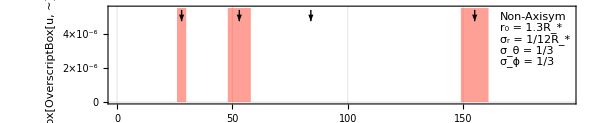

```mathematica
sgr[1900]={28,53,84,155};
sgrs={2,5,0,6};
ymax=0.0000055(*0.016*);
sgrplot=Show[ListLinePlot[Table[{(*10*)(sgr[1900][[i]]+(-1)^j sgrs[[i]]),21.11},{i,Length[sgr[1900]]},{j,2}],PlotRange->{{0,195(*1650*)},{0,ymax(*21*)}},
PlotStyle->Directive[PointSize[0.001]],
ImageSize->600,AspectRatio->1/(3GoldenRatio),
Filling->Axis,FillingStyle->Directive[Thickness[.03],RGBColor[1,0.32,0.25,0.55]],
(*PlotLabel->Style["External Origin",FontSize->14],*)
LabelStyle->{Directive[Black,FontFamily->Times,FontSize->12]},
GridLines->{zshift(2π τ)^-1 Flatten[Table[Re[ww[n,l]],{l,1,25},{n,1,20}]], {0}},
Frame->True,FrameTicksStyle->Directive[RGBColor[0,0,0],Thickness[.0015]],FrameStyle->Directive[Black,Thickness[.002]],
FrameLabel->{"Frequency [Hz]"(*""*),"(│ SubscriptBox[OverscriptBox[u, ~], s] │)/(R_*) √E_0"},
FrameTicks->{{(*Left*)leftticksEx,(*Right*)Table[If[Mod[x,10/10000000(*5/1000*)]==0,{x,"",{.015,0}},{x,"",{.005,0}}],{x,0,55/10000000(*20/1000*),2/10000000(*1/1000*)}]},{(*Bottom*)Table[If[Mod[x, 50]==0,{x,ToString[x],{.015,0}},{x,"",{.005,0}}],{x,0,190,10}],(*Top*)Table[If[Mod[x, 50]==0,{x,"",{.015,0}},{x,"",{.005,0}}],{x,0,190,10}]}}],
Graphics[{Thick,Arrowheads[.02],
Arrow[{{sgr[1900][[1]],.98 ymax},{sgr[1900][[1]],.86ymax}}],
Arrow[{{sgr[1900][[2]],.98 ymax},{sgr[1900][[2]],.86ymax}}],
Arrow[{{sgr[1900][[3]],.98 ymax},{sgr[1900][[3]],.86ymax}}],
Arrow[{{sgr[1900][[4]],.98 ymax},{sgr[1900][[4]],.86ymax}}]}],
Graphics[{White,Rectangle[{165,.36(*.78*)ymax},{191.5(*260*),.98ymax}]}],
Graphics[{Directive[Black,FontFamily->Times,FontSize->12],
Text["Non-Axisym"(*"Axisymmetric"*),{166,.85ymax},{-1,-1}],
Text["r_0 = 1.3R_*",{166,.73ymax},{-1,-1}],
Text["σ_r = 1/12R_*",{166,.61ymax},{-1,-1}],
Text["σ_θ = 1/3",{166,.49ymax},{-1,-1}],
Text["σ_ϕ = 1/3",{166,.37ymax},{-1,-1}]}]]
```

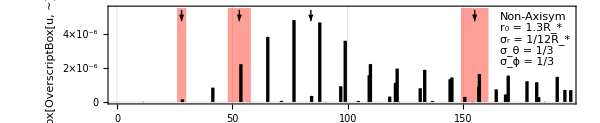

```mathematica
(* ... *)
Show[sgrplot,ListPlot[Table[{zshift(2π τ)^-1 Re[ww[n,l]],Abs[(l(l+1)(π c2 μ2)/(2 Re[ww[n,l]]^2)A1[l,Re[ww[n,l]]]A2[l,Re[ww[n,l]]])^-1 π Im[ww[n,l]]uamp abe[n,l](Sum[(TH1[l,m]PH1[m]+TH2[l,m]PH2[m])Evaluate[D[SphericalHarmonicY[l,m,θ,ϕ], θ]]/.{θ->θp,ϕ->ϕp},{m,-l,l}]) Re[A2[l,Re[ww[n,l]]]SphericalHankelH1[l,rp Re[ww[n,l]]/c2]]]^1},
{l,lmn,lmx},{n,1,10}],
PlotRange->{{1,195},{0,0.0000055}},Filling->Axis,FillingStyle->Directive[Thickness[.004],Black],PlotStyle->Directive[PointSize[.0001],Black]]]
```

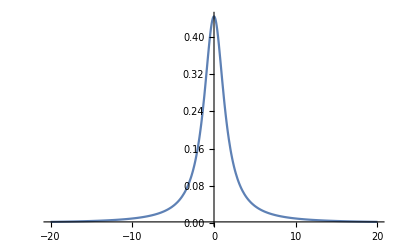

```mathematica
Plot[1/(x^2+(1/2 3)^2),{x,-20,20},PlotRange->All]
```

```mathematica
NIntegrate[1/(x^2+(1/2 5)^2),{x,-200,200}]
2π/5.
```

1.24664

1.25664

```mathematica
PolyhedronData["DodecahedronSmallTriambicIcosahedronCompound"]
```

-Graphics3D-